## Playing with the Discrete Fourier Transform

Defining the size of the samples we are going to use in this experiment.

```mathematica
s=200
```

200

Defining a simple sine wave function and plotting a mixed test.

```mathematica
x[f_,n_]:=Sin[(2*Pi*f*n)/s]
```

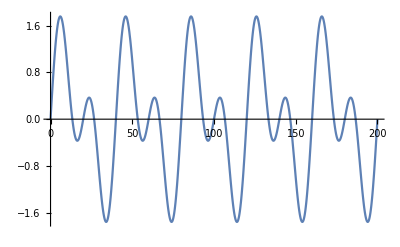

```mathematica
Plot[x[5,n]+x[10,n],{n,0,s}]
```

Defining the frequency function we’ll use to beat agaisnt the sampled wave.

```mathematica
Wk[f_,n_]:=(2*Pi*f*n)/s
```

Plotting some simple DFTs to check if everything is working as we’ve expected.

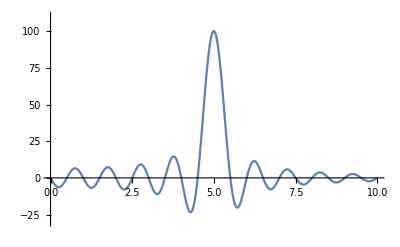

```mathematica
Plot[Sum[x[5,n]*Sin[Wk[f,n]],{n,0,s}],{f,0,10},PlotRange->{-30,110}]
```

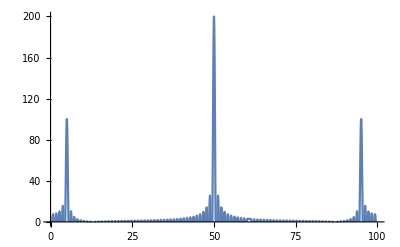

```mathematica
Plot[Sum[(x[5,n]+2*x[50,n]+x[95,n])*Sin[Wk[f,n]],{n,0,s}],{f,0,100},PlotRange->{0,200}]
```